```mathematica
(* Start with V = const *)
```

```mathematica
s=NDSolve[{-(x'[t])^2+(x[t])^2(y'[t])^2+(x[t])^2 1==0,y''[t]+(3 x'[t]y'[t])/x[t]+0==0,x[.001]==.114471, y[.001]==-1,y'[.001]==100},{x,y},{t,.005,2}]
```

NDSolve::ndsz: At t == 0.00433328, step size is effectively zero; singularity or stiff system suspected.

NDSolve`ProcessSolutions::nodata: No solution data was computed between t == 0.005 and t == 2..

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…]}}

InterpolatingFunction::dmval: Input value {0.00204082} lies outside the range of data in the interpolating function. Extrapolation will be used.

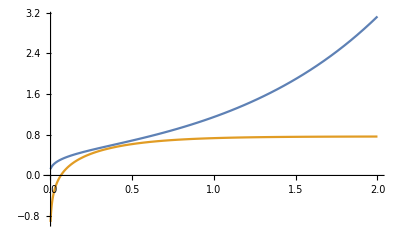

```mathematica
Plot[Evaluate[{x[t],y[t]}/.s],{t,.002,2}]
```

```mathematica
(* now try v = phi^2 *)
```

```mathematica
s=NDSolve[{-(x'[t])^2+(x[t])^2(y'[t])^2+(x[t])^2(y[t])^2==0,y''[t]+(3 x'[t]y'[t])/x[t]+y[t]==0,x[.001]==.114471, y[.001]==-1,y'[.001]==100},{x,y},{t,.005,2}]
```

NDSolve::ndsz: At t == 0.00433326, step size is effectively zero; singularity or stiff system suspected.

NDSolve`ProcessSolutions::nodata: No solution data was computed between t == 0.005 and t == 2..

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…]}}

InterpolatingFunction::dmval: Input value {0.00204082} lies outside the range of data in the interpolating function. Extrapolation will be used.

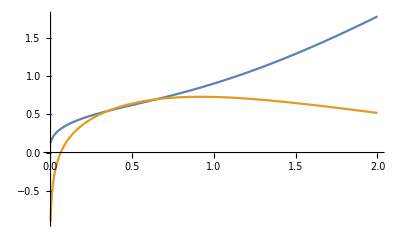

```mathematica
Plot[Evaluate[{x[t],y[t]}/.s],{t,.002,2}]
```

```mathematica
(* Let's try V(phi) 1 + 2 phi^2 *)
```

```mathematica
s=NDSolve[{-(x'[t])^2+(x[t])^2(y'[t])^2+(x[t])^2(1+2(y[t])^2)==0,y''[t]+(3 x'[t]y'[t])/x[t]+2y[t]==0,x[.001]==.114471, y[.001]==-1,y'[.001]==100},{x,y},{t,.005,2}]
```

NDSolve::ndsz: At t == 0.00433323, step size is effectively zero; singularity or stiff system suspected.

NDSolve`ProcessSolutions::nodata: No solution data was computed between t == 0.005 and t == 2..

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…]}}

InterpolatingFunction::dmval: Input value {0.00204082} lies outside the range of data in the interpolating function. Extrapolation will be used.

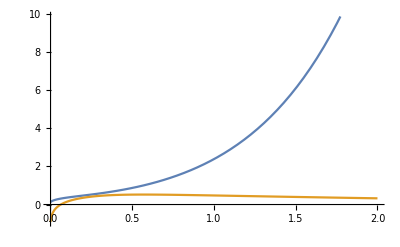

```mathematica
Plot[Evaluate[{x[t],y[t]}/.s],{t,.002,2}]
```

```mathematica
(*Starobinsky potential *)
```

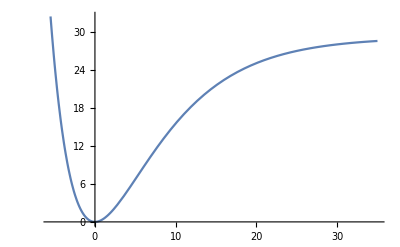

```mathematica
Plot[7/(48(.005)) (ⅇ^(-x/7.637626158259733)-1)^2,{x,-5.5,35}]
```

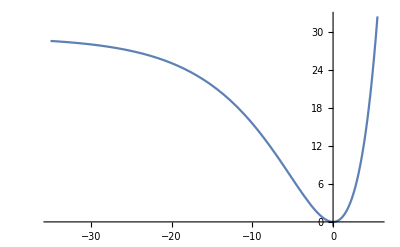

```mathematica
Plot[7/(48(.005)) (ⅇ^(x/7.637626158259733)-1)^2,{x,-35,5.5}]
```

```mathematica
Series[7/(48(.005)) (ⅇ^(x/7.637626158259733)-1)^2,{x,0,4}]
```

```mathematica
0.49999999999999994 x^2+0.06546536707079771 x^3+0.004999999999999999 x^4+O[x]^5

D[(7/(48(.005)) (ⅇ^(x/7.637626158259733)-1)^2), x]
```

7.63763 ⅇ^(0.130931 x) (-1+ⅇ^(0.130931 x))

```mathematica
Series[7.637626158259733 ⅇ^(0.13093073414159542 x) (-1+ⅇ^(0.13093073414159542 x)),{x,0,3}]
```

x+0.196396 x^2+0.02 x^3+O[x]^4

```mathematica
s=NDSolve[{-(x'[t])^2+(x[t])^2(y'[t])^2+(x[t])^2 2(7/(48(.005)) (ⅇ^(y[t]/7.637626158259733)-1)^2)==0,y''[t]+(3 x'[t]y'[t])/x[t]+(7.637626158259733 ⅇ^(0.13093073414159542 y[t]) (-1+ⅇ^(0.13093073414159542 y[t])))==0,x[.001]==.114471, y[.001]==-1,y'[.001]==100},{x,y},{t,.005,2}]
```

NDSolve::ndsz: At t == 0.00433327, step size is effectively zero; singularity or stiff system suspected.

NDSolve`ProcessSolutions::nodata: No solution data was computed between t == 0.005 and t == 2..

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…]}}

InterpolatingFunction::dmval: Input value {0.00204082} lies outside the range of data in the interpolating function. Extrapolation will be used.

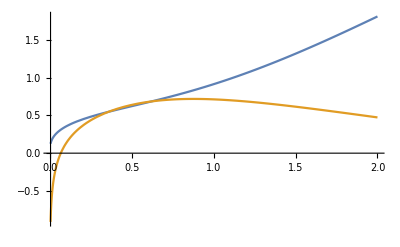

```mathematica
Plot[Evaluate[{x[t],y[t]}/.s],{t,.002,2}]
```